# Fundamental Solution

## Deriving the fundamental solution of the strongly damped wave equation

```mathematica
k[ω_]:=ω/Sqrt[1-ⅈ ω];
F[r_,ω_]:=Exp[ⅈ k[ω] r +ⅈ ω]/(4π r(1-ⅈ ω));
```

```mathematica
R = 5;
r= 1;
A = ComplexPlot3D[F[r,ω],{ω,-R-R ⅈ,R+R ⅈ},PlotRange->{0,3*10^0},Boxed->False,AxesOrigin->{0,0,0},Mesh->False,AxesStyle->{Black,Black,Black},AxesEdge->{Automatic,Automatic,None},Ticks->None,
RegionFunction->Function[{ω},Abs[ω]<R],ColorFunction->Automatic,AxesLabel->{Style["Re",Italic,20,FontFamily->"Times"],Style["Im",Italic,20,FontFamily->"Times"]}];
B=ParametricPlot3D[{x,0,Abs[F[r,x]]},{x,-R,R},PlotStyle->{Black,Dashed,Thick,Specularity[White]}];
Show[A,B]
```

-Graphics3D-

```mathematica
ComplexPlot3D[Exp[+ⅈ ω],{ω,-2-2ⅈ,2+4ⅈ},PlotRange->Automatic]
```

-Graphics3D-

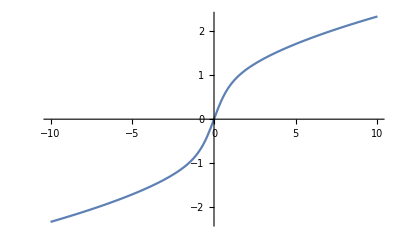

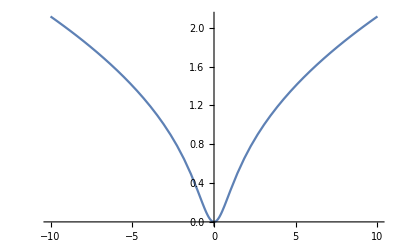

```mathematica
Plot[Re[x/Sqrt[1-ⅈ x]],{x,-10,10}]
Plot[Im[x/Sqrt[1-ⅈ x]],{x,-10,10}]
```

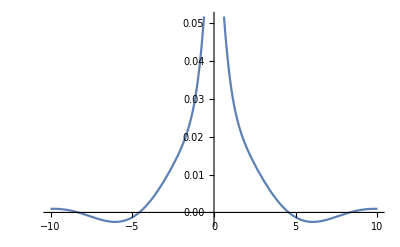

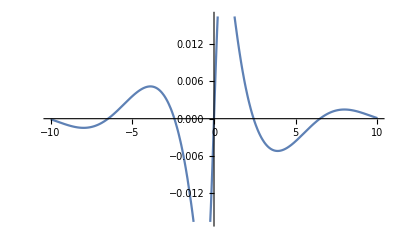

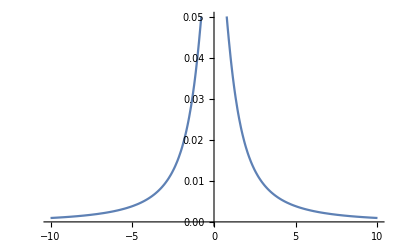

```mathematica
Plot[Re[F[1,x]],{x,-10,10}]
Plot[Im[F[1,x]],{x,-10,10}]
Plot[Abs[F[1,x]],{x,-10,10}]
```

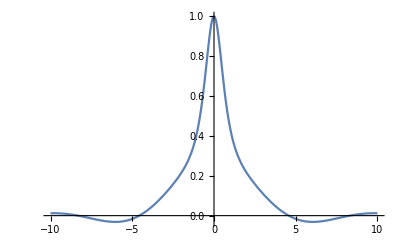

```mathematica
f[ω_,r_,t_]:=Exp[-Im[k[ω]] r]/(1+ω^2) (Cos[Re[k[ω]]r-ω t] - ω Sin[Re[k[ω]]r - ω t]);
Plot[f[x,1,1],{x,-10,10},PlotRange->All]
```

```mathematica
Manipulate[Plot[2*NIntegrate[f[ω,r,t],{ω,0,Infinity}],{r,10^(-1),5}],{{t,1},10^(-1),10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {83.8619}. NIntegrate obtained 1.06331+0. ⅈ and 0.228326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {68.1055}. NIntegrate obtained -0.0528151+0. ⅈ and 0.206757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {186.315}. NIntegrate obtained 0.13528+0. ⅈ and 0.172518 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {205.705}. NIntegrate obtained 0.0126347+0. ⅈ and 0.222114 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {205.38}. NIntegrate obtained 0.877105+0. ⅈ and 0.15181 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {253.438}. NIntegrate obtained 2.07355+0. ⅈ and 0.0852775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {321.009}. NIntegrate obtained 1.44977+0. ⅈ and 0.067278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {205.217}. NIntegrate obtained 0.251987+0. ⅈ and 0.154765 for the integral and error estimates.

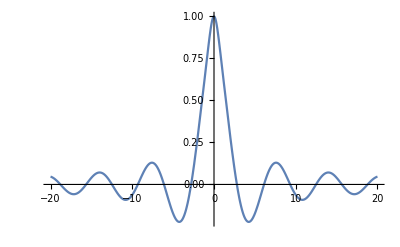

ConditionalExpression[(ⅇ^(-√(t^2)) π (t+√(t^2)))/t, Im[t]≤0]

```mathematica
P1 = Plot[(Cos[x] + x Sin[x])/(1+x^2),{x,-20,20},PlotRange->All]
Integrate[(Cos[x t] + x Sin[x t])/(1+x^2),{x,-Infinity,Infinity}]
```